```mathematica
Subscript[rho, crit] = 1.5*10^-7; 
f = 0.1;
p = 1.9;
c= 10;
G = 0.0045;
k = 2;
Mprimary = 10^12;
```

Masses in solar mass, distances in pc, times in Myr

```mathematica
MaxRadius[M_]:=  (3 M/(4 Pi *200 * Subscript[rho, crit]))^(1/3)
Subscript[RhoFree, nfw][r_, M_] := Module[{Rmax =MaxRadius[M]},Module[{ Rc = Rmax / c}, 200/3 Subscript[rho, crit]/(Log[1+c] - c/(1+c))c^3If[r < Rmax, 1/(r/Rc*(1+r/Rc)^2), 0]]]
Subscript[MFree, nfw][r_, M_] := Module[{Rmax = MaxRadius[M]},Module[{ Rc = Rmax / c}, M*If[r < Rmax, (Log[1+r/Rc]-r/(r+Rc))/(Log[1+c] - c/(1+c)), 1]]]
Subscript[PhiFree, nfw][r_, M_] := Module[{Rmax = MaxRadius[M]},Module[{ Rc = Rmax / c}, -M*G/Rmax*If[r < Rmax, (Rmax/r * Log[1+r/Rc]-Log[1+c])/(Log[1+c]-c/(1+c)) + 1, Rmax/r]]]
Subscript[N, halo][M_, R_] := M^-p  *Subscript[RhoFree, nfw][R, Mprimary]  * (2-p) f^(p-1) Mprimary^(p-2)

TidalRadius[m_,R_]:= R*(m/(2*Subscript[MFree, nfw][R,Mprimary]))^(1/3)
Truncate[m_, R_]:= Subscript[MFree, nfw][TidalRadius[m,R],m]

TidalRadius2[m_,R_]:= If[MaxRadius[m] > R*(m/(2*Subscript[MFree, nfw][R,Mprimary]))^(1/3), Sqrt[R^3*(m/(2*Subscript[MFree, nfw][R,Mprimary]))/MaxRadius[m]], R*(m/(2*Subscript[MFree, nfw][R,Mprimary]))^(1/3)]

LeeTruncate[m_, R_]:= If[1/2 (4Pi /3 200 Subscript[rho, crit])m/Mprimary R^3 < m, 1/2 (4Pi /3 200 Subscript[rho, crit])m/Mprimary R^3, m]

Subscript[MSubHalo, nfw][r_, M_, R_] := Module[{Rmax = Min[TidalRadius[M,R], MaxRadius[M]]},Module[{ Rc = MaxRadius[M] / c}, (k-1)*M If[r < Rmax, (Log[1+r/Rc]-r/(r+Rc))/(Log[1+c] - c/(1+c)), (Log[1+Rmax/Rc]-Rmax/(Rmax+Rc))/(Log[1+c] - c/(1+c))]]]

PotChange[m_,R_,r_]:=If[r> 0, Subscript[MSubHalo, nfw][r, m, R] *G/r^2, 0]
```

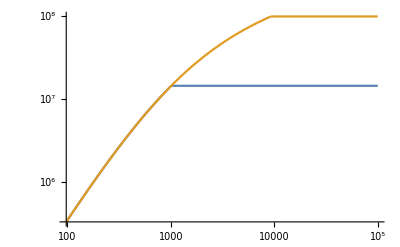

```mathematica
FlucExact[D_]:=NIntegrate[2Pi  R^2 Sin[theta] * Subscript[N, halo][m, R]*(PotChange[m,R,Sqrt[D^2+R^2-2D R Cos[theta]]])^2 * (-Subscript[PhiFree, nfw][R, Mprimary]/3),{R, 0, D/2},{theta,0,Pi}, {m, 0, f Mprimary}]

LogLogPlot[{Subscript[MSubHalo, nfw][r, 10^8, 10^4], Subscript[MFree, nfw][r, 10^8]},{r,0,10^5}]
```

```mathematica
Fluc[D_]:=NIntegrate[4Pi  R^2  * Subscript[N, halo][m, D]*(PotChange[m,D,R])^2 * (-Subscript[PhiFree, nfw][D, Mprimary]/3),{R, 0, D/2},{m, 0, f Mprimary}]
```

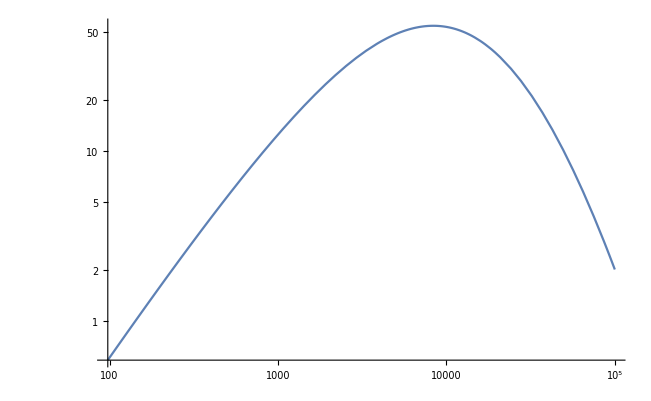

```mathematica
LogLogPlot[Fluc[x], {x, 0 ,10^5}]
```

```mathematica
NatrualNormalize[R_]:= (Subscript[PhiFree, nfw][R, Mprimary])^2* 4Pi Subscript[MFree, nfw][R, Mprimary]/R^3;
```

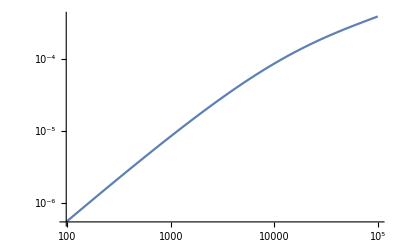

```mathematica
NormedFluc[D_]:= Fluc[D]/NatrualNormalize[D];
LogLogPlot[Sqrt[NormedFluc[x]], {x, 0 ,10^5}]
```

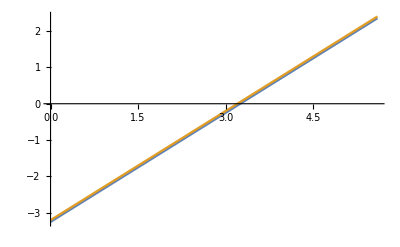

```mathematica
Plot[{Log10[Truncate[10^x, 10^0]] ,x-3.2}, {x,0 ,5.6}]
```

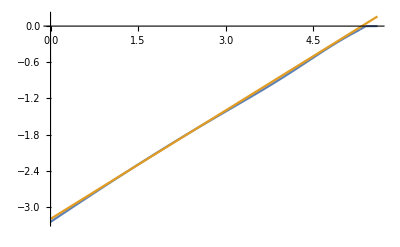

```mathematica
Plot[{Log10[Truncate[10^0, 10^x]] ,-3.2+ 0.6 x}, {x,0 ,5.6}]
```

mass in halos goes as r^0.6

```mathematica
Plot3D[{Log10[Truncate[10^x, 10^y]], If[y < Log10[MaxRadius[Mprimary]],x+0.6y-3.2, x]}, {x,0, 9}, {y, 0, 7}]
```

-Graphics3D-

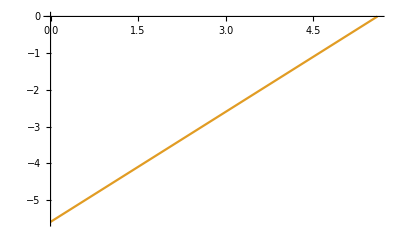

```mathematica
Plot[{Log10[Truncate2[10^0, 10^x]] ,-5.6+  x}, {x,0 ,5.6}]
```

```mathematica
Plot3D[{Log10[Truncate2[10^x, 10^y]], If[y < Log10[MaxRadius[Mprimary]],x+y-5.6, x]}, {x,0, 9}, {y, 0, 7}]
```

-Graphics3D-

```mathematica
Plot3D[{Log10[LeeTruncate[10^x, 10^y]], If[y < Log10[MaxRadius[Mprimary]],x+3y-16.2, x]}, {x,0, 9}, {y, 0, 7}]
```

-Graphics3D-

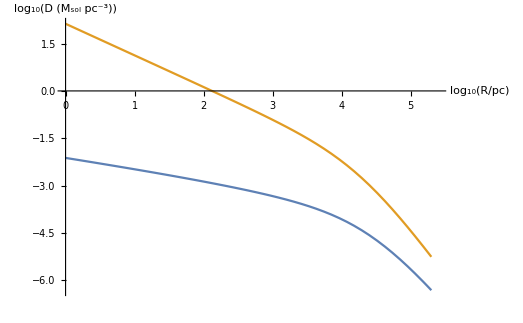

```mathematica
HaloDensity[R_] := NIntegrate[Truncate[m,R]*Subscript[N, halo][m, R], {m, 0, f Mprimary}]
Plot[{Log10[HaloDensity[10^x]],Log10[Subscript[RhoFree, nfw][10^x, Mprimary]]},{x,0, 5.4}, AxesLabel->{"log_10(R/pc)","log_10(D (M_sol pc^-3))"}, BaseStyle->{FontSize->14}]
```

```mathematica
Subscript[RhoFree, nfw][10^3, Mprimary]/HaloDensity[10^3]
```

261.14

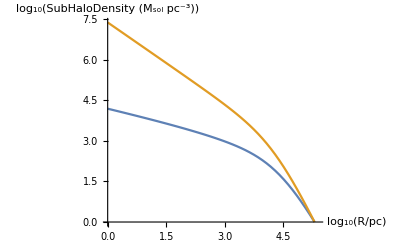

```mathematica
Quiet[Plot[{Log10[HaloDensity[10^x]/HaloDensity[MaxRadius[Mprimary]-1]],Log10[Subscript[RhoFree, nfw][10^x, Mprimary]/Subscript[RhoFree, nfw][MaxRadius[Mprimary]-1, Mprimary]]},{x,0, 5.4}, AxesLabel->{"log_10(R/pc)","log_10(SubHaloDensity (M_sol pc^-3))"}, BaseStyle->{FontSize->14}] ]
```

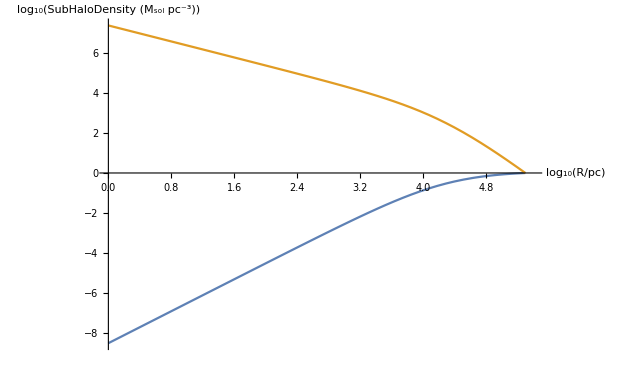

```mathematica
HaloDensity[R_] := NIntegrate[LeeTruncate[m,R]*Subscript[N, halo][m, R], {m, 0, f Mprimary}]
Quiet[Plot[{Log10[HaloDensity[10^x]/HaloDensity[MaxRadius[Mprimary]-1]],Log10[Subscript[RhoFree, nfw][10^x, Mprimary]/Subscript[RhoFree, nfw][MaxRadius[Mprimary]-1, Mprimary]]},{x,0, 5.4}, AxesLabel->{"log_10(R/pc)","log_10(SubHaloDensity (M_sol pc^-3))"}, BaseStyle->{FontSize->14}] ]
```

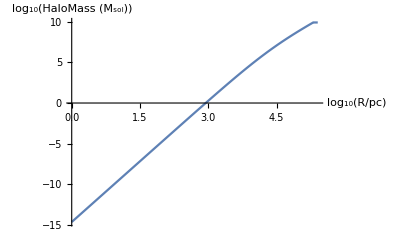

```mathematica
HaloMass[R_]:= Quiet[NIntegrate[4Pi r^2 HaloDensity[r], {r,0, R}]]
Plot[{Log10[HaloMass[10^x]]},{x,0, 5.4}, AxesLabel->{"log_10(R/pc)","log_10(HaloMass (M_sol))"}, BaseStyle->{FontSize->14}]
```

```mathematica
HaloMass[MaxRadius[Mprimary]]/Mprimary
```

0.00855219

fraction of primary mass in halos

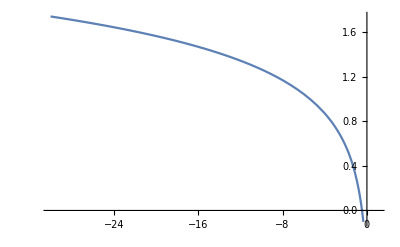

```mathematica
FourierFunction[k_]:= N[Sqrt[2/Pi] BesselK[0, Abs[k]]]
FourierIntegral[k_]:= N[Pi/2 (1/k- BesselK[0, k] StruveL[-1,k] - BesselK[0, k] StruveL[0, k])]
Plot[Log10[FourierFunction[10^t]], {t,-30, 1}]
```

```mathematica
FourierMag[D_, O_]:= NIntegrate[4Pi  R^2  * Subscript[N, halo][m, D]* Subscript[MSubHalo, nfw][R, m, D] *G/(Sqrt[- 2 Pi Subscript[PhiFree, nfw][D, Mprimary]]) *  FourierFunction[R O /Sqrt[-  Subscript[PhiFree, nfw][D, Mprimary]]],{R, 0, D/2},{m, 0, f Mprimary}]
```

```mathematica
NormedFourierMag[D_, O_]:= NIntegrate[4Pi  R^2  * Subscript[N, halo][m, D]* Subscript[MSubHalo, nfw][R, m, D] *G/Sqrt[2 Pi] *  FourierFunction[R O Sqrt[Subscript[MFree, nfw][D,Mprimary ] *G/D^3]/Sqrt[-  Subscript[PhiFree, nfw][D, Mprimary]/3]],{R, 0, D/2},{m, 0, f Mprimary}]/-Subscript[PhiFree, nfw][D, Mprimary] * Sqrt[Subscript[MFree, nfw][D,Mprimary ] *G/D^3]/Sqrt[-  Subscript[PhiFree, nfw][D, Mprimary]/3]
```

```mathematica
NormedFourierMagInt[D_]:= NIntegrate[4Pi  R^2  * Subscript[N, halo][m, D]* Subscript[MSubHalo, nfw][R, m, D] *G/Sqrt[2 Pi] *  FourierIntegral[R Sqrt[Subscript[MFree, nfw][D,Mprimary ] *G/D^3]/Sqrt[-  Subscript[PhiFree, nfw][D, Mprimary]/3]],{R, 0, D/2},{m, 0, f Mprimary}]/-Subscript[PhiFree, nfw][D, Mprimary] * Sqrt[Subscript[MFree, nfw][D,Mprimary ] *G/D^3]/Sqrt[-  Subscript[PhiFree, nfw][D, Mprimary]/3]
```

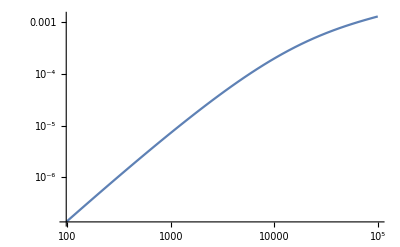

```mathematica
Quiet[LogLogPlot[NormedFourierMagInt[x], {x, 0, 10^5}]]
```

```mathematica
tab = Quiet[Table[{n/5, Log10[NormedFourierMagInt[10^(n/5)]]}, {n, 0, 25}]];
```

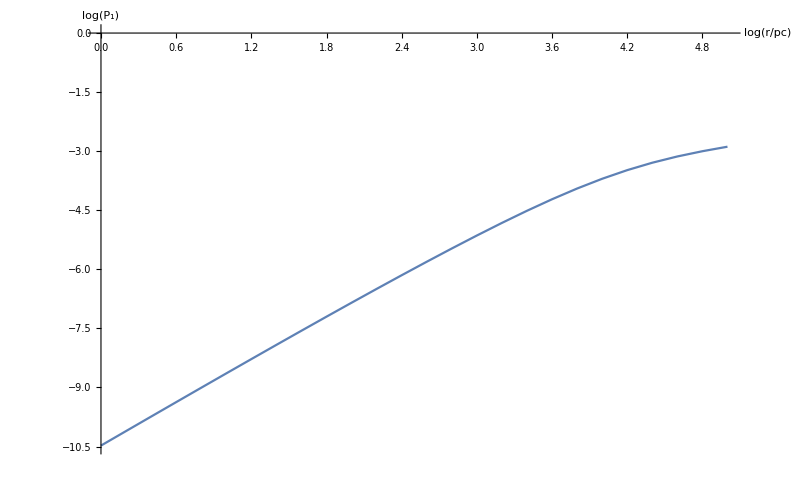

```mathematica
ListPlot[tab, AxesLabel->{"log(r/pc)","log(P_1)"}, LabelStyle->Directive[Black, Medium], Joined->True]
```

```mathematica
SubHaloTidalForce[r_, m_, D_]:=  Module[{Rmax = Min[TidalRadius[m,D], MaxRadius[m]]},Module[{ Rc = MaxRadius[m]/ c}, (k-1)*m G*If[r < 10^-1, 2/(3 Rc^3)/(Log[1+c] - c/(1+c)), 1/r^3 If[r < Rmax, (2Log[1+r/Rc]-r(3r+2Rc)/(r+Rc)^2)/(Log[1+c] - c/(1+c)), 2 Truncate[m, D]/m]]]]

HaloTidalForce[r_, m_, D_]:=  Module[{Rmax = MaxRadius[m]},Module[{ Rc = MaxRadius[m]/ c}, (k-1)*m G*If[r < 10^-1, 2/(3 Rc^3)/(Log[1+c] - c/(1+c)), 1/r^3 If[r < Rmax, (2Log[1+r/Rc]-r(3r+2Rc)/(r+Rc)^2)/(Log[1+c] - c/(1+c)), 2 ]]]]
```

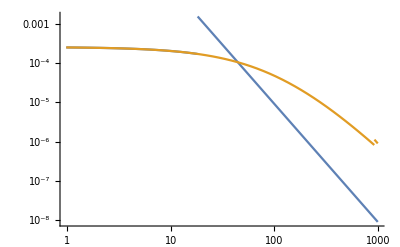

```mathematica
LogLogPlot[{SubHaloTidalForce[x, 10^5, 10^2], HaloTidalForce[x, 10^5, 10^2]}, {x, 0 , 1000}]
```

```mathematica
TidalVariance[D_]:= NIntegrate[4Pi R^2  Subscript[N, halo][m, D] (SubHaloTidalForce[R, m, D])^2, {R, 0.2, D/2},{m, 1, f Mprimary}]/(2 Subscript[MFree, nfw][D, Mprimary] G / D^3 - 4 Pi Subscript[RhoFree, nfw][D, Mprimary] G)^2
```

```mathematica
logtidaltab = Quiet[Table[{n/5, Log10[TidalVariance[10^(n/5)]]}, {n, 0, 40}]];
```

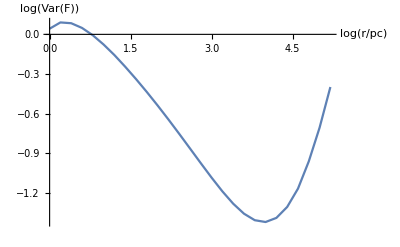

```mathematica
ListPlot[logtidaltab,  AxesLabel->{"log(r/pc)","log(Var(F))"}, LabelStyle->Directive[Black, Medium], Joined->True]
```